```mathematica
t0[x_] = (Sin[(x-Pi)/2] * Sin[(x - 7Pi/4)/2]) / ((-1)* Sin[-7Pi/8])
```

Csc[π/8] Sin[1/2 (-(7 π)/4+x)] Sin[1/2 (-π+x)]

```mathematica
t1[x_] = (Sin[(x)/2] * Sin[(x - 7Pi/4)/2]) / Sin[-3Pi/8]
```

-Sec[π/8] Sin[x/2] Sin[1/2 (-(7 π)/4+x)]

```mathematica
t2[x_] = (Sin[x/2] * Sin[(x - Pi)/2]) / (Sin[7Pi/8]*Sin[3Pi/8])
```

Csc[π/8] Sec[π/8] Sin[x/2] Sin[1/2 (-π+x)]

```mathematica
L[x_] = 5t1[x] + 9t2[x]
```

-5 Sec[π/8] Sin[x/2] Sin[1/2 (-(7 π)/4+x)]+9 Csc[π/8] Sec[π/8] Sin[x/2] Sin[1/2 (-π+x)]

```mathematica
L[x] //Simplify
```

-Sec[π/8] Sin[x/2] (9 Cos[x/2] Csc[π/8]+5 Sin[1/8 (-7 π+4 x)])

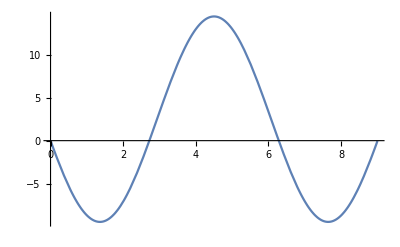

```mathematica
Plot[Simplify[L[x]], {x, 0, 9}]
```

```mathematica
Plot[L[x], {x, 0, 9}]
```

-Graphics-

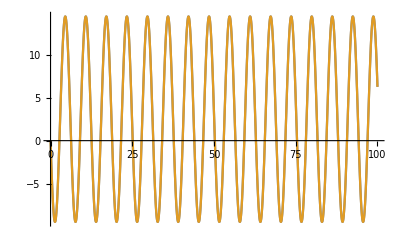

```mathematica
Plot[{L[x],Simplify[L[x]]}, {x, 0, 100}]
```

```mathematica
ListPlot[Simplify[L[x]], {x, 0, 9}]
```

ListPlot::nonopt: Options expected (instead of {x, 0, 9}) beyond position 1 in ListPlot[-Sec[π/8]\ Sin[x/2]\ (9\ Cos[x/2]\ Csc[π/8] + 5\ Sin[1/8\ (Times[« 2 »] + Times[« 2 »])]), {x, 0, 9}]. An option must be a rule or a list of rules.

ListPlot[-Sec[π/8] Sin[x/2] (9 Cos[x/2] Csc[π/8]+5 Sin[1/8 (-7 π+4 x)]),{x,0,9}]

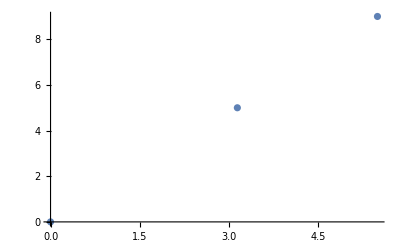

```mathematica
ListPlot[{{0, 0} ,{Pi, 5}, {7Pi/4, 9}}]
```

```mathematica
Plot[{L[x], ListPlot[{{0, 0} ,{Pi, 5}, {7Pi/4, 9}}]}, {x, 0, 9}]
```

-Graphics-

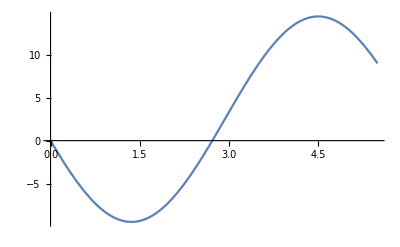

```mathematica
Plot[Simplify[L[x]], {x, 0, 7Pi/4}]
```

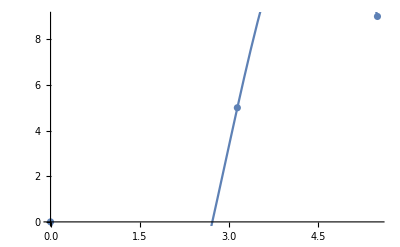

```mathematica
Show[ListPlot[{{0, 0} ,{Pi, 5}, {7Pi/4, 9}}], Plot[Simplify[L[x]], {x, 0, 7Pi/4}]]
```

```mathematica
Show[ListPlot[{{0, 0} ,{Pi, 5}, {7Pi/4, 9}}], Plot[Simplify[L[x]], {x, 0, 7Pi/4}], Range -> All]
```

-Graphics-

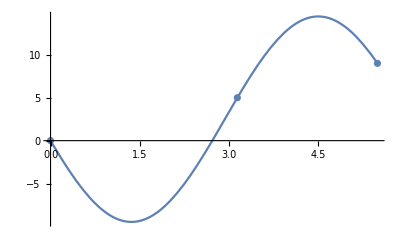

```mathematica
Show[ListPlot[{{0, 0} ,{Pi, 5}, {7Pi/4, 9}}], Plot[Simplify[L[x]], {x, 0, 7Pi/4}], PlotRange -> All]
```

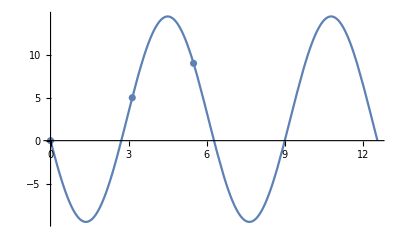

```mathematica
Show[ListPlot[{{0, 0} ,{Pi, 5}, {7Pi/4, 9}}], Plot[Simplify[L[x]], {x, 0, 4Pi}], PlotRange -> All]
```

```mathematica
P[x_] = -1 + (x+2) + 3(x+2)(x-1) + (x+2)(x-1)(x-4)
```

1+x+3 (-1+x) (2+x)+(-4+x) (-1+x) (2+x)

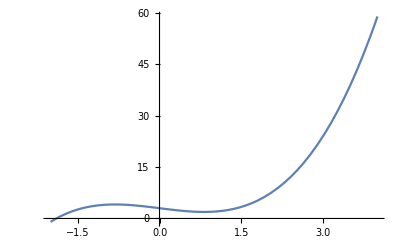

```mathematica
Plot[Simplify[P[x]], {x, -2, 4}]
```

```mathematica
P[-1]
```

4

```mathematica
P[1]
```

2

```mathematica
P[4]
```

59

```mathematica
P[-2]
```

-1